```mathematica
(* uloha 1 *)
U=12+7ⅉ;
Abs[U]//N(* fazor, amplituda *)
Arg[U]//N(* velikost uhlu *)
```

13.8924

0.528074

```mathematica
U=14+8ⅉ;
Abs[U]//N (* fazor, amplituda *)
Arg[U]//N (* velikost uhlu *)
```

16.1245

0.519146

```mathematica
(* uloha 2 *)
U=15;
f=15*ⅇ^(ⅉ*(Pi/3))//N (* == 15 * Exp[ⅉ*(Pi/3)] *)
I1=4.8;
f=I1*Exp[ⅉ*1.2]
```

7.5+12.9904 ⅈ

1.73932+4.47379 ⅈ

```mathematica
(* uloha 3 *)
9.2*Exp[ⅉ*2.4]
```

-6.78402+6.21426 ⅈ

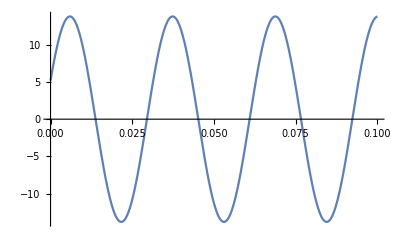

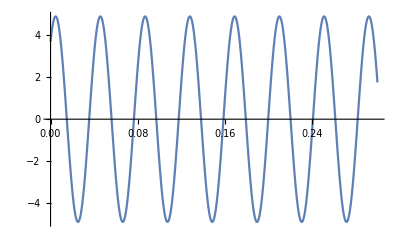

```mathematica
(* uloha 4 *)
Plot[Im[(12.8+5.2ⅉ)*Exp[ⅉ*200*t]], {t, 0, 0.1}]
Plot[Im[(3.2+3.7ⅉ)*Exp[ⅉ*153*t]], {t, 0, 0.3}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

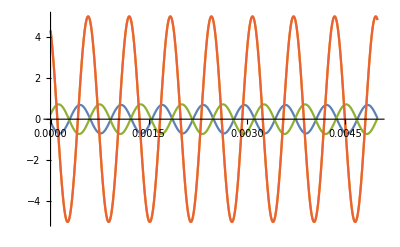

```mathematica
R=1000;
C1=1*10^-6;
uZf=5*Exp[ⅉ*2.1];
ω=10^4;

uzel1 = iUf== iRf;
uzel2 = iRf== iCf;
rovR1=u1f-u2f==R*iRf;
rovC= iCf==u2f*C1*u2f*ⅉ*ω;
rovU = u1f==uZf;

rce = {uzel1, uzel2, rovR1, rovC, rovU};
vysledek =Solve[rce];
Plot[Evaluate[{Im[u2f*Exp[ⅉ*ω*t]], Im[u1f*Exp[ⅉ*ω*t]]}/.vysledek], {t, 0, 0.005}]
```